# Mathematica Bootcamp: Step 3

전경원 박사

Machine Learning Research Engineer
(주)시정
ruddyscent@gmail.com

2021년 10월 18일 월요일

## Access to Lecture Materials

최신 자료는 아래 링크에서 내려받으실 수 있습니다.

https://github.com/ruddyscent/mathematica-bootcamp-2021

## References

체험하며 배우는 WOLFRAM MATHEMATICA
-Graphics-

Wolfram 언어 기초 입문
-Graphics-

Hands-on Start to Mathematica Online, Wolfram U
https://www.wolfram.com/wolfram-u/hands-on-start-to-mathematica-online/

## Wolfram Language

## Syntax Coloring

```mathematica
Expand[
```

```mathematica
Expand[]]
```

```mathematica
DateString[]
```

Wed 20 Oct 2021 16:41:38

```mathematica
Range[1,2,3,3]
```

Range::argb: Range called with 4 arguments; between 1 and 3 arguments are expected.

Range[1,2,3,3]

```mathematica
Expand[]
```

Expand::argt: Expand called with 0 arguments; 1 or 2 arguments are expected.

Expand[]

Expandd[(x+1)^10]

Expandd[(1+x)^10]

Expand[

Expand[]]

```mathematica
Range[2,12,3]
```

{2,5,8,11}

Range[]

Range::argb: Range called with 0 arguments; between 1 and 3 arguments are expected.

Range[]

Range[2,12,3,1]

Range::argb: Range called with 4 arguments; between 1 and 3 arguments are expected.

Range[2,12,3,1]

## 참값과 근삿값

718을 3으로 나눈값은?

```mathematica
718/3
```

718/3

```mathematica
π
```

π

718을 3으로 나누었을 때의 근삿값은?

```mathematica
N[718/3*1.1234567,2]
```

268.881

```mathematica
N[718/3,10]
```

239.3333333

```mathematica
718/3.
```

239.333

## List

```mathematica
{1,2,3,1.,1/23,"가나다","abc",CurrentImage[]}
```

{1,2,3,1.,1/23,가나다,abc,-Graphics-}

```mathematica
{1,a,"가나다",CurrentImage[],{}}
```

{1,a,가나다,-Graphics-,{}}

## 1부터 10까지의 자연수

```mathematica
{1,2,3}
```

{1,2,3}

```mathematica
{1,2,3,4,5,6,7,8,9,10}
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[2,10,2]
```

{2,4,6,8,10}

Range[10]

{1,2,3,4,5,6,7,8,9,10}

Range[1, 10]

{1,2,3,4,5,6,7,8,9,10}

Range[1, 10, 3]

{1,4,7,10}

## 1부터 100까지 제곱수의 목록

```mathematica
{1^2}
```

{1}

```mathematica
{1^2,2^2}
```

{1,4}

```mathematica
{1^2,2^2,3^2,4^2,5^2,6^2,7^2,8^2,9^2,10^2}
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[i^2,{i,0,10,2}]
```

{0,4,16,36,64,100}

```mathematica
Table[1,10]
```

{1,1,1,1,1,1,1,1,1,1}

Table[i^2,{i,10}]

{1,4,9,16,25,36,49,64,81,100}

Table[i^2,{i,0,10}]

{0,1,4,9,16,25,36,49,64,81,100}

Table[i^2,{i,0,10,2}]

{0,4,16,36,64,100}

Table[{i,i^2},{i,10}]

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

Table[π,10]

{π,π,π,π,π,π,π,π,π,π}

## 함수

```mathematica
((1+x)+y)*z
```

(1+x+y) z

```mathematica
{}
```

{}

```mathematica
f(x)
```

f x

```mathematica
f[x,y]
```

f[x,y]

```mathematica
myX
```

myX

```mathematica
mySin[x]
```

mySin[x]

```mathematica
Sin[1]
```

Sin[1]

Sin[π]

0

전위 형식

```mathematica
f@x
```

f[x]

Sin@π

0

후위 형식

```mathematica
x//Sin//Exp
```

ⅇ^Sin[x]

```mathematica
x//f
```

f[x]

π//Sin

0

## 합성함수.1c

```mathematica
g[f[x]]
```

g[f[x]]

Sin[Sin[π]]

0

전위 형식

```mathematica
g@f@x
```

g[f[x]]

Sin@Sin@π

0

후위 형식

```mathematica
x//f//g
```

g[f[x]]

x // Sin // Sin

Sin[Sin[x]]

## 순수함수

```mathematica
f[x]
```

f[x]

```mathematica
#^2&
```

#1^2&

Evaluate

```mathematica
f[1]
```

f[1]

```mathematica
Sin[1]
```

Sin[1]

```mathematica
#^2&[2]
```

4

전위 형식

```mathematica
(#^2+1)&@2
```

5

```mathematica
#^2&@2
```

4

후위 형식

```mathematica
2//#^2&
```

4

## Rule

```mathematica
x=2
x^2
```

2

4

```mathematica
x=.
```

```mathematica
x->2
```

x→2

```mathematica
x^2/.x->2
```

4

```mathematica
->
```

```mathematica
x->2
```

x→2

x^2/.x→2

4

```mathematica
Table[(x+i)^2,{i,10}]
%/.x->0
%%/.x->1
```

{(1+x)^2,(2+x)^2,(3+x)^2,(4+x)^2,(5+x)^2,(6+x)^2,(7+x)^2,(8+x)^2,(9+x)^2,(10+x)^2}

{1,4,9,16,25,36,49,64,81,100}

{4,9,16,25,36,49,64,81,100,121}

```mathematica
%%%
```

{(1+x)^2,(2+x)^2,(3+x)^2,(4+x)^2,(5+x)^2,(6+x)^2,(7+x)^2,(8+x)^2,(9+x)^2,(10+x)^2}

Table[(x+i)^2,{i,10}]
%/.x→0

{(1+x)^2,(2+x)^2,(3+x)^2,(4+x)^2,(5+x)^2,(6+x)^2,(7+x)^2,(8+x)^2,(9+x)^2,(10+x)^2}

{1,4,9,16,25,36,49,64,81,100}

{f[x],g[x]}
%/.{f→(#^2&),g→(Sin[#]&)}

{f[x],g[x]}

{x^2,Sin[x]}

## Algebraic Manipulation

## 기본 연산

```mathematica
1+2
```

3

상쇄

```mathematica
(2 a b)/(b c)
```

(2 a)/c

전개

```mathematica
(a+b)(a+c)(b+c)
%//Expand
%//Factor
```

(a+b) (a+c) (b+c)

a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2

(a+b) (a+c) (b+c)

Expand[(a+b)(a+c)(b+c)]

a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2

인수분해

```mathematica
a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2
```

a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2

Factor[a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2]

(a+b) (a+c) (b+c)

## 분수

통분

```mathematica
1/(x+1)+1/(x-1)//Together//Apart
```

1/(-1+x)+1/(1+x)

```mathematica
1/(x+1)+1/(x-1)
```

1/(-1+x)+1/(1+x)

Together[1/(x+1)+1/(x-1)]

(2 x)/((-1+x) (1+x))

분수 분해

```mathematica
(2 x)/((-1+x) (1+x))
```

(2 x)/((-1+x) (1+x))

Apart[(2 x)/((-1+x) (1+x))]

1/(-1+x)+1/(1+x)

항의 정리

```mathematica
a x^2+b x^2+c x y
Collect[%,{x,y}]
```

a x^2+b x^2+c x y

(a+b) x^2+c x y

Collect[a x^2+b x^2 y+c x y^2,x]

c x y^2+x^2 (a+b y)

Collect[a x^2+b x^2 y+c x y^2,y]

a x^2+b x^2 y+c x y^2

## 삼각함수

수식 정리

```mathematica
Sin[x]^2+Cos[x]^2//FullSimplify
```

1

Sin[x]^2+Cos[x]^2//Simplify

1

```mathematica
Simplify[√(x^2),x>0]
```

x

```mathematica
Simplify[√(x^2)]
```

√(x^2)

Simplify[√(x^2),x>0]

x

삼각함수의 조작

```mathematica
Sin[x^2]+Cos[2 x]//TrigExpand
%//Simplify
```

Cos[x]^2-Sin[x]^2+Sin[x^2]

Cos[2 x]+Sin[x^2]

TrigExpand[Sin[x^2]+Cos[2 x]]

Cos[x]^2-Sin[x]^2+Sin[x^2]

TrigReduce[Cos[x]^2-Sin[x]^2+Sin[x^2]]

Cos[2 x]+Sin[x^2]

Cos[x]^2-Sin[x]^2+Sin[x^2]//Simplify

Cos[2 x]+Sin[x^2]

```mathematica
ⅇ^x//Series[#,{x,1,3}]&
```

ⅇ+ⅇ (x-1)+1/2 ⅇ (x-1)^2+1/6 ⅇ (x-1)^3+O[x-1]^4

## 방정식의 풀이

방정식의 풀이

```mathematica
x^2+2x-1==0
Solve[%,x]
```

-1+2 x+x^2==0

{{x→-1-√2},{x→-1+√2}}

```mathematica
x^2+2x-1==0/.x->-1+√2
```

True

```mathematica
x^2+2x-1==0
Reduce[%,x]
```

-1+2 x+x^2==0

x==-1-√2||x==-1+√2

Solve[x^2+2x-1==0,x]

{{x→-1-√2},{x→-1+√2}}

연립방정식의 풀이

```mathematica
{2x+y==12,x+4y==34}
Solve[%,{x,y}]
```

{2 x+y==12,x+4 y==34}

{{x→2,y→8}}

```mathematica
{2x+y==12,x+4y==34}
```

{2 x+y==12,x+4 y==34}

Solve[{2x+y==12,x+4y==34},{x,y}]

{{x→2,y→8}}

일반적 풀이 구하기

```mathematica
Solve[x^2-y^3==1,y]
```

{{y→(-1+x^2)^(1/3)},{y→-(-1)^(1/3) (-1+x^2)^(1/3)},{y→(-1)^(2/3) (-1+x^2)^(1/3)}}

Reduce[x^2-y^3==1,{x,y}]

y==(-1+x^2)^(1/3)||y==-(-1)^(1/3) (-1+x^2)^(1/3)||y==(-1)^(2/3) (-1+x^2)^(1/3)

수치해 구하기

```mathematica
Sin[x^2]-Cos[x]==0
```

-Cos[x]+Sin[x^2]==0

Plot[Sin[x^2]-Cos[x],{x,0,10}]

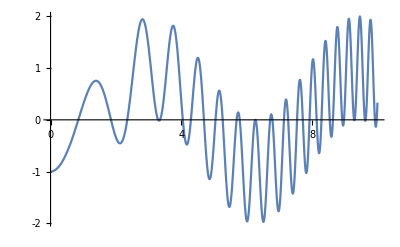

```mathematica
DateString[];
```

```mathematica
Solve[Sin[x^2]-Cos[x]==0,x];
%/.C[1]->0
```

{{x→1/2 (-1-√(1+2 π))},{x→1/2 (1-√(1+2 π))},{x→1/2 (-1+√(1+2 π))},{x→1/2 (1+√(1+2 π))},{x→1/2 (-1-ⅈ √(-1+6 π))},{x→1/2 (1-ⅈ √(-1+6 π))},{x→1/2 (-1+ⅈ √(-1+6 π))},{x→1/2 (1+ⅈ √(-1+6 π))}}

Solve[Sin[x^2]-Cos[x]==0,x]
%/.C[1]→-1//N

{{x→ConditionalExpression[1/2 (-1-√(1+2 π-16 π C[1])), C[1]∈ℤ]},{x→ConditionalExpression[1/2 (1-√(1+2 π-16 π C[1])), C[1]∈ℤ]},{x→ConditionalExpression[1/2 (-1+√(1+2 π-16 π C[1])), C[1]∈ℤ]},{x→ConditionalExpression[1/2 (1+√(1+2 π-16 π C[1])), C[1]∈ℤ]},{x→ConditionalExpression[1/2 (-1-√(1+2 π-8 (π+2 π C[1]))), C[1]∈ℤ]},{x→ConditionalExpression[1/2 (1-√(1+2 π-8 (π+2 π C[1]))), C[1]∈ℤ]},{x→ConditionalExpression[1/2 (-1+√(1+2 π-8 (π+2 π C[1]))), C[1]∈ℤ]},{x→ConditionalExpression[1/2 (1+√(1+2 π-8 (π+2 π C[1]))), C[1]∈ℤ]}}

{{x→-4.29304},{x→-3.29304},{x→3.29304},{x→4.29304},{x→-3.34675},{x→-2.34675},{x→2.34675},{x→3.34675}}

FindRoot[Sin[x^2]-Cos[x],{x,π}]

{x→3.29304}

예제

```mathematica
x+ⅇ^x==1/2
```

ⅇ^x+x==1/2

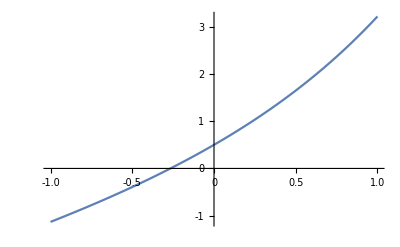

```mathematica
Plot[x+ⅇ^x-1/2,{x,-1,1}]
```

```mathematica
Solve[x+ⅇ^x==1/2,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/2 (1-2 ProductLog[√ⅇ])}}

```mathematica
Reduce[x+ⅇ^x==1/2,x]
%/.C[1]->0
%//N
```

C[1]∈ℤ&&x==1/2-ProductLog[C[1],√ⅇ]

x==1/2-ProductLog[√ⅇ]

x==-0.266249

```mathematica
FindRoot[x+ⅇ^x-1/2,{x,0}]
```

{x→-0.266249}